```mathematica
SetDirectory[NotebookDirectory[]];
Needs["MaTeX`"];
color1=RGBColor[0.12156862745098039,0.4666666666666667,0.7058823529411765];
color2=RGBColor[0.7372549019607844,0.7411764705882353,0.13333333333333333];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];
psPL=Import["./data/SurvivalProbability_R_PL.txt","Table","FieldSeparators"->",",HeaderLines->1];
psNFW=Import["./data/SurvivalProbability_R_NFW.txt","Table","FieldSeparators"->",",HeaderLines->1];
minX=0;
maxX=2;
minY=-0.5;
maxY=1.5;
LTL=0.04;
STL=0.02;
ftickX=frameThicksLinear[minX,maxX,longT->LTL,shortT->STL,writeValues->True,numberInterval->1,longTickInterval->1,tickInterval->0.2];
ftickY=frameThicksLinear[minY,maxY,longT->LTL,shortT->STL,writeValues->True,numberInterval->1,longTickInterval->1,tickInterval->0.2];
ftickTop=frameThicksLinear[minX,maxX,longT->LTL,shortT->STL,writeValues->False,numberInterval->1,longTickInterval->1,tickInterval->0.2];
ftickRight=frameThicksLinear[minY,maxY,longT->LTL,shortT->STL,writeValues->False,numberInterval->1,longTickInterval->1,tickInterval->0.2];
ltPL=Length[psPL];
rtPL=Table[0,{i,1,ltPL}];
survprobcutPL=Table[0,{i,1,ltPL}];
Do[{rtPL[[i]]=10^-3 psPL[[i,1]];
survprobcutPL[[i]]=psPL[[i,6]]/psPL[[i,3]];},{i,1,ltPL}];
fPL=survprobcutPL[[ltPL]];
tablePL=Table[{rtPL[[i]],survprobcutPL[[i]]},{i,1,ltPL}];
psurvPL=Interpolation[tablePL,"ExtrapolationHandler"->{If[#≤tablePL[[1,1]],0,fPL]&,"WarningMessage"->False}];
ltNFW=Length[psNFW];
rtNFW=Table[0,{i,1,ltNFW}];
survprobcutNFW=Table[0,{i,1,ltNFW}];
Do[{rtNFW[[i]]=10^-3 psNFW[[i,1]];
survprobcutNFW[[i]]=psNFW[[i,6]]/psNFW[[i,3]];},{i,1,ltNFW}];
fNFW=survprobcutNFW[[ltNFW]];
tableNFW=Table[{rtNFW[[i]],survprobcutNFW[[i]]},{i,1,ltNFW}];
psurvNFW=Interpolation[tableNFW,"ExtrapolationHandler"->{If[#≤tableNFW[[1,1]],0,fNFW]&,"WarningMessage"->False}];
protonmass=1.78 10^-24;
MSun=2 10^33;
MSunGeV=MSun/protonmass;
days=86400;
kpc=3.086 10^21;
rhoDMSun=0.45;
rsun=8.33;
rsMW=16.1;
g1=1-1.7;
ma=25 10^-6;
mmin=5.1 10^-10(ma/10^-10)^(-3/2)(1.8/7.5)^2;
mmax=4.9 10^6 6.6 10^-12(ma/10^-5)^(-1/2);
HMF[M_]:=(g1 M^g1)/(mmax^g1-mmin^g1);
Mavg=NIntegrate[HMF[M],{M,mmin,mmax}];
```

```mathematica
FrameM31=LogPlot[10^-40,{x,0,1},PlotRange->{{0,1},{0.9 10^18,10^24}},Frame->True,Axes->False,AspectRatio->1/1.5,FrameStyle->Directive[Thickness[0.003],FontSize->15,FontFamily->"Times",Black],LabelStyle->{{FontFamily->"Helvetica"},{FontFamily->"Helvetica"}},FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"x","n_{\\rm AMC}\\,[{\\rm kpc^{-3}}]","",""},FrameTicks->{ftickX,ftickY,ftickTop,ftickRight},PlotRangeClipping->True,PlotRangePadding->None,ImagePadding->{{True,10},{True,10}},
ImageSize->350]
```

-Graphics-

```mathematica
(*M31*)
Ds=780;(*kpc*)
l=121.2 π/180;
b=-21.6 π/180;
rs=25;
rhoDM=4.96 10^6 MSun/protonmass;
rMW[x_]:=√(rsun^2-2rsun Ds x Cos[l]Cos[b]+Ds^2 x^2);
rM31[x_]:=(1-x)Ds;
nMW[r_,M_]:=(rhoDMSun kpc^3)/(1+r/rsMW)^2 1/(M MSunGeV)rsun/r(1+rsun/rsMW)^2;
nMWPL[r_,M_]:=fPL nMW[r,M];
nMWNFW[r_,M_]:=fNFW nMW[r,M];
nMWPL10[r_,M_]:=psurvPL[r]nMW[r,M];
nMWNFW10[r_,M_]:=psurvNFW[r]nMW[r,M];
nM31[r_,M_]:=rhoDM/(1+r/rs)^2 1/(M MSunGeV)rs/r;
nM31PL[r_,M_]:=fPL nM31[r,M];
nM31NFW[r_,M_]:=fNFW nM31[r,M];
nM31PL10[r_,M_]:=psurvPL[r rsMW/rs]nM31[r,M];
nM31NFW10[r_,M_]:=psurvNFW[r rsMW/rs]nM31[r,M];
prof[x_,M_]:=nMW[rMW[x],M]+nM31[rM31[x],M];
profPL[x_,M_]:=nMWPL[rMW[x],M]+nM31PL[rM31[x],M];
profNFW[x_,M_]:=nMWNFW[rMW[x],M]+nM31NFW[rM31[x],M];
profPL10[x_,M_]:=nMWPL10[rMW[x],M]+nM31PL10[rM31[x],M];
profNFW10[x_,M_]:=nMWNFW10[rMW[x],M]+nM31NFW10[rM31[x],M];
profavg[x_]:=NIntegrate[HMF[M]/M prof[x,M],{M,mmin,mmax},MaxRecursion->12];
profavgPL[x_]:=NIntegrate[HMF[M]/M profPL[x,M],{M,mmin,mmax},MaxRecursion->12];
profavgNFW[x_]:=NIntegrate[HMF[M]/M profNFW[x,M],{M,mmin,mmax},MaxRecursion->12];
profavgPL10[x_]:=NIntegrate[HMF[M]/M profPL10[x,M],{M,mmin,mmax},MaxRecursion->12];
profavgNFW10[x_]:=NIntegrate[HMF[M]/M profNFW10[x,M],{M,mmin,mmax},MaxRecursion->12];
rg[M_]:=9.72 10^-14 M;
thetaE[x_,M_]:=√((2rg[M])/Ds x(1-x));
vE[x_,M_,t_]:=(2 1.34  thetaE[x,M] Ds x)/t;
v0=220/(3.086 10^16);(*kpc/s*)
T[x_,M_]:=(2 1.34  thetaE[x,M] Ds x)/v0;
Nstar=5.49 10^6;
Tobs=2500 days;
Eps=0.5;
tI=120;
tF=7 3600;
Nexp[t_,M_]:=NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 prof[x,M] ((ⅇ^(-(T[x,M]/t)^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,1}];
NexpPL[t_,M_]:=NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 profPL[x,M] ((ⅇ^(-T[x,M]^2/t^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,0.95}];
NexpNFW[t_,M_]:=NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 profNFW[x,M] ((ⅇ^(-T[x,M]^2/t^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,0.95}];
NexpPL10[t_,M_]:=NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 profPL10[x,M] ((ⅇ^(-T[x,M]^2/t^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,0.95}];
NexpNFW10[t_,M_]:=NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 profNFW10[x,M] ((ⅇ^(-T[x,M]^2/t^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,0.95}];
NU[M_]:=Nexp[tF,M]-Nexp[tI,M];
NPL[M_]:=NexpPL[tF,M]-NexpPL[tI,M];
NNFW[M_]:=NexpNFW[tF,M]-NexpNFW[tI,M];
NPL10[M_]:=NexpPL10[tF,M]-NexpPL10[tI,M];
NNFW10[M_]:=NexpNFW10[tF,M]-NexpNFW10[tI,M];
nu=NU[Mavg];
nPL=NPL[Mavg];
nNFW=NNFW[Mavg];
nPL10=NPL10[Mavg];
nNFW10=NNFW10[Mavg];
Abs[(nPL10-nPL)/nPL]
Abs[(nNFW10-nNFW)/nNFW]
texStyle={FontFamily->"Latin Modern Roman",FontSize->14};
(*inset=LogPlot[{profavg[x],profavgPL[x],profavgNFW[x],profavgPL10[x],profavgNFW10[x]},{x,0,0.05},PlotRange->{{0,0.05},{0.5 10^24,5 10^25}},Frame->True,Axes->False,PlotStyle->{{Black},{color1},{color2},{color1,DotDashed},{color2,DotDashed}},FrameStyle->Directive[6]];*)
(*PlotM31=
Show[MyFrame,Graphics[{Rectangle[{0,Log[10^21]},{1,Log[10^26]},p1],Rectangle[{0.16,Log[10^22.5]},{0.81,Log[10^26.5]},inset]}],Graphics[Text[Style["M31",FontFamily->"Times",FontSize->12],{0.5,Log[10^25.7]}]]]*)
```

0.00340883

0.0155715

```mathematica
NexpPL[t_,M_]:=NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 profPL[x,M] ((ⅇ^(-T[x,M]^2/t^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,1}];
NexpNFW[t_,M_]:=NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 profNFW[x,M] ((ⅇ^(-T[x,M]^2/t^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,1}];
NexpPL10[t_,M_]:=NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 profPL10[x,M] ((ⅇ^(-T[x,M]^2/t^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,1}];
NexpNFW10[t_,M_]:=NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 profNFW10[x,M] ((ⅇ^(-T[x,M]^2/t^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,1}];
```

```mathematica
p1=LogPlot[{profavgPL[x],profavgNFW[x],profavgPL10[x],profavgNFW10[x]},{x,0,1},PlotRange->{{0,1},{10^17,10^25}},Axes->False,Frame->False,PlotStyle->{{color1,DotDashed},{color2,DotDashed},{color1},{color2}}];
```

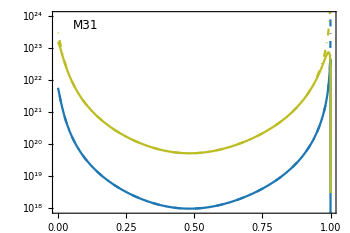

../../draft/figures/PlotM31.pdf

```mathematica
PlotM31=
Show[FrameM31,p1,Graphics[Text[Style["M31",FontFamily->"Times",FontSize->12],{0.1,Log[10^23.68]}]]]
Export["../../draft/figures/PlotM31.pdf",PlotM31]
```

```mathematica
(*LMC*)
Ds=48;(*kpc*)
l=280.46 π/180;
b=-32.89 π/180;
rs=12.6;
rhoDM=2.6 10^6 MSun/protonmass;
rMW[x_]:=√(rsun^2-2rsun Ds x Cos[l]Cos[b]+Ds^2 x^2);
rM31[x_]:=(1-x)Ds;
nMW[r_,M_]:=(rhoDMSun kpc^3)/(1+r/rsMW)^2 1/(M MSunGeV)rsun/r(1+rsun/rsMW)^2;
nMWPL[r_,M_]:=fPL nMW[r,M];
nMWNFW[r_,M_]:=fNFW nMW[r,M];
nMWPL10[r_,M_]:=psurvPL[r]nMW[r,M];
nMWNFW10[r_,M_]:=psurvNFW[r]nMW[r,M];
nM31[r_,M_]:=rhoDM/(1+r/rs)^2 1/(M MSunGeV)rs/r;
nM31PL[r_,M_]:=fPL nM31[r,M];
nM31NFW[r_,M_]:=fNFW nM31[r,M];
nM31PL10[r_,M_]:=psurvPL[r rsMW/rs]nM31[r,M];
nM31NFW10[r_,M_]:=psurvNFW[r rsMW/rs]nM31[r,M];
prof[x_,M_]:=nMW[rMW[x],M]+nM31[rM31[x],M];
profPL[x_,M_]:=nMWPL[rMW[x],M]+nM31PL[rM31[x],M];
profNFW[x_,M_]:=nMWNFW[rMW[x],M]+nM31NFW[rM31[x],M];
profPL10[x_,M_]:=nMWPL10[rMW[x],M]+nM31PL10[rM31[x],M];
profNFW10[x_,M_]:=nMWNFW10[rMW[x],M]+nM31NFW10[rM31[x],M];
profavg[x_]:=NIntegrate[HMF[M]/M prof[x,M],{M,mmin,mmax},MaxRecursion->12];
profavgPL[x_]:=NIntegrate[HMF[M]/M profPL[x,M],{M,mmin,mmax},MaxRecursion->12];
profavgNFW[x_]:=NIntegrate[HMF[M]/M profNFW[x,M],{M,mmin,mmax},MaxRecursion->12];
profavgPL10[x_]:=NIntegrate[HMF[M]/M profPL10[x,M],{M,mmin,mmax},MaxRecursion->12];
profavgNFW10[x_]:=NIntegrate[HMF[M]/M profNFW10[x,M],{M,mmin,mmax},MaxRecursion->12];
rg[M_]:=9.72 10^-14 M;
thetaE[x_,M_]:=√((2rg[M])/Ds x(1-x));
vE[x_,M_,t_]:=(2 1.34  thetaE[x,M] Ds x)/t;
v0=220/(3.086 10^16);(*kpc/s*)
T[x_,M_]:=(2 1.34  thetaE[x,M] Ds x)/v0;
Nstar=5.49 10^6;
Tobs=2500 days;
Eps=0.5;
tI=120;
tF=7 3600;
Nexp[t_,M_]:=NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 prof[x,M] ((ⅇ^(-(T[x,M]/t)^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,0.9}];
NexpPL[t_,M_]:=NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 profPL[x,M] ((ⅇ^(-T[x,M]^2/t^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,0.9}];
NexpNFW[t_,M_]:=NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 profNFW[x,M] ((ⅇ^(-T[x,M]^2/t^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,0.9}];
NexpPL10[t_,M_]:=NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 profPL10[x,M] ((ⅇ^(-T[x,M]^2/t^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,0.9}];
NexpNFW10[t_,M_]:=NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 profNFW10[x,M] ((ⅇ^(-T[x,M]^2/t^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,0.9}];
NU[M_]:=Nexp[tF,M]-Nexp[tI,M];
NPL[M_]:=NexpPL[tF,M]-NexpPL[tI,M];
NNFW[M_]:=NexpNFW[tF,M]-NexpNFW[tI,M];
NPL10[M_]:=NexpPL10[tF,M]-NexpPL10[tI,M];
NNFW10[M_]:=NexpNFW10[tF,M]-NexpNFW10[tI,M];
nu=NU[Mavg];
nPL=NPL[Mavg];
nNFW=NNFW[Mavg];
nPL10=NPL10[Mavg];
nNFW10=NNFW10[Mavg];
Abs[(nPL10-nPL)/nPL]
Abs[(nNFW10-nNFW)/nNFW]
```

0.00885438

0.188999

```mathematica
p2=LogPlot[{profavgPL[x],profavgNFW[x],profavgPL10[x],profavgNFW10[x]},{x,0,1},PlotRange->{{0,1},{10^20,10^25}},Frame->True,Axes->False,PlotStyle->{{color1,DotDashed},{color2,DotDashed},{color1},{color2}},AspectRatio->1/1.5,FrameStyle->Directive[Thickness[0.003],FontSize->15,FontFamily->"Times",Black],FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"x","n_{\\rm AMC}\\,[{\\rm kpc^{-3}}]","",""},FrameTicks->{ftickX,ftickY,ftickTop,ftickTop},PlotRangeClipping->True,PlotRangePadding->None,ImagePadding->{{True,10},{10,10}},
ImageSize->350,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}}];
```

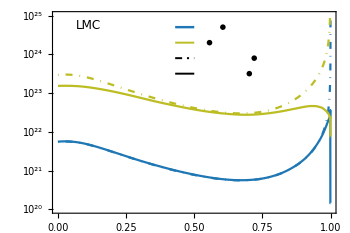

../../draft/figures/PlotLMC.pdf

```mathematica
Labels=LogPlot[{10^24.7,10^24.3,10^23.9,10^23.5},{x,0.43,0.5},PlotStyle->{{color1,Thickness[0.005]},{color2,Thickness[0.004]},{Black, AbsoluteDashing[{5,3.5,1.5,3.5}],Thickness[0.004]},{Black,Thickness[0.004]}}];
PlotLMC=Show[p2,Graphics[{EdgeForm[Thin],White,Opacity[0.7],Rectangle[{0.42,Log[10^23.3]},{0.93,Log[10^24.85]}]}],Labels,Graphics[Text[Style["LMC",FontFamily->"Times",FontSize->12],{0.112,Log[10^24.73]}]],Graphics[Text[MaTeX["{\\rm Power-law}",Magnification->0.8],{0.605,Log[10^24.7]}]],Graphics[Text[MaTeX["{\\rm NFW}",Magnification->0.8],{0.556,Log[10^24.3]}]],Graphics[Text[MaTeX["{\\rm Unperturbed \\,AMCs + AS \\, cut}",Magnification->0.8],{0.72,Log[10^23.9]}]],Graphics[Text[MaTeX["{\\rm Perturbed \\,AMCs + AS \\, cut}",Magnification->0.8],{0.702,Log[10^23.5]}]]]
Export["../../draft/figures/PlotLMC.pdf",PlotLMC]
```

```mathematica
(*Bulge*)
Ds=rsun;(*kpc*)
l=1.09 π/180;
b=-2.39 π/180;
rMW[x_]:=rsun √(1-2 x Cos[l]Cos[b]+x^2);
rM31[x_]:=(1-x)Ds;
nMW[r_,M_]:=(rhoDMSun kpc^3)/(1+r/rsMW)^2 1/(M MSunGeV)rsun/r(1+rsun/rsMW)^2;
nMWPL[r_,M_]:=fPL nMW[r,M];
nMWNFW[r_,M_]:=fNFW nMW[r,M];
nMWPL10[r_,M_]:=psurvPL[r]nMW[r,M];
nMWNFW10[r_,M_]:=psurvNFW[r]nMW[r,M];
prof[x_,M_]:=nMW[rMW[x],M];
profPL[x_,M_]:=nMWPL[rMW[x],M];
profNFW[x_,M_]:=nMWNFW[rMW[x],M];
profPL10[x_,M_]:=nMWPL10[rMW[x],M];
profNFW10[x_,M_]:=nMWNFW10[rMW[x],M];
profavg[x_]:=NIntegrate[HMF[M]/M prof[x,M],{M,mmin,mmax},MaxRecursion->12];
profavgPL[x_]:=NIntegrate[HMF[M]/M profPL[x,M],{M,mmin,mmax},MaxRecursion->12];
profavgNFW[x_]:=NIntegrate[HMF[M]/M profNFW[x,M],{M,mmin,mmax},MaxRecursion->12];
profavgPL10[x_]:=NIntegrate[HMF[M]/M profPL10[x,M],{M,mmin,mmax},MaxRecursion->12];
profavgNFW10[x_]:=NIntegrate[HMF[M]/M profNFW10[x,M],{M,mmin,mmax},MaxRecursion->12];
rg[M_]:=9.72 10^-14 M;
thetaE[x_,M_]:=√((2rg[M])/Ds x(1-x));
vE[x_,M_,t_]:=(2 1.34  thetaE[x,M] Ds x)/t;
v0=220/(3.086 10^16);(*kpc/s*)
T[x_,M_]:=(2 1.34  thetaE[x,M] Ds x)/v0;
Nstar=5.49 10^6;
Tobs=2500 days;
Eps=0.5;
tI=120;
tF=7 3600;
Nexp[t_,M_]:=Quiet[NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 prof[x,M] ((ⅇ^(-(T[x,M]/t)^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,1}]];
NexpPL[t_,M_]:=Quiet[NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 profPL[x,M] ((ⅇ^(-T[x,M]^2/t^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,1}]];
NexpNFW[t_,M_]:=Quiet[NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 profNFW[x,M] ((ⅇ^(-T[x,M]^2/t^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,1}]];
NexpPL10[t_,M_]:=Quiet[NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 profPL10[x,M] ((ⅇ^(-T[x,M]^2/t^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,1}]];
NexpNFW10[t_,M_]:=Quiet[NIntegrate[Nstar Tobs Ds (v0 T[x,M])^2 profNFW10[x,M] ((ⅇ^(-T[x,M]^2/t^2))/t-(√π)/(2T[x,M]) Erf[T[x,M]/t]),{x,0,1}]];
NU[M_]:=Nexp[tF,M]-Nexp[tI,M];
NPL[M_]:=NexpPL[tF,M]-NexpPL[tI,M];
NNFW[M_]:=NexpNFW[tF,M]-NexpNFW[tI,M];
NPL10[M_]:=NexpPL10[tF,M]-NexpPL10[tI,M];
NNFW10[M_]:=NexpNFW10[tF,M]-NexpNFW10[tI,M];
nu=NU[Mavg];
nPL=NPL[Mavg];
nNFW=NNFW[Mavg];
nPL10=NPL10[Mavg];
nNFW10=NNFW10[Mavg];
Abs[(nPL10-nPL)/nPL]
Abs[(nNFW10-nNFW)/nNFW]
```

0.114457

0.920331

```mathematica
Framebulge=LogPlot[10^-40,{x,0,1},PlotRange->{{0,1},{10^21,10^26}},PlotStyle->{Black},Frame->True,Axes->False,AspectRatio->1/1.5,FrameStyle->Directive[Thickness[0.003],FontSize->15,FontFamily->"Times",Black],LabelStyle->{{FontFamily->"Helvetica"},{FontFamily->"Helvetica"}},FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"x","n_{\\rm AMC}\\,[{\\rm kpc^{-3}}]","",""},PlotRangeClipping->True,PlotRangePadding->None,ImagePadding->{{True,10},{10,10}},
ImageSize->350,FrameTicks->{ftickX,ftickY,ftickTop,ftickTop},FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}}]
```

-Graphics-

```mathematica
plotbulge=LogPlot[{profavgPL[x],profavgNFW[x],profavgPL10[x],profavgNFW10[x]},{x,0,1},PlotRange->{{0,1},{10^20,10^26}},PlotStyle->{{color1,DotDashed},{color2,DotDashed},{color1},{color2}}];
```

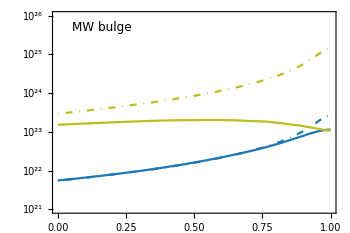

../../draft/figures/Plotbulge.pdf

```mathematica
Plotbulge=Show[Framebulge,plotbulge,Graphics[Text[Style["MW bulge",FontFamily->"Times",FontSize->12],{0.16,Log[10^25.7]}]]]
Export["../../draft/figures/Plotbulge.pdf",Plotbulge]
```

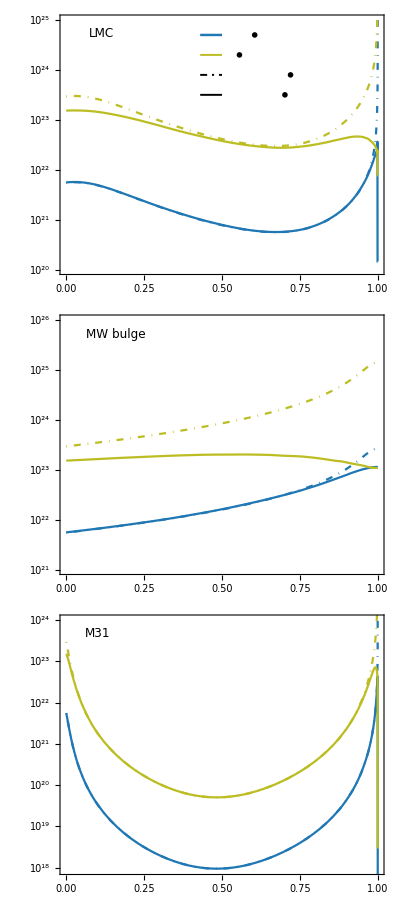

../../draft/figures/Plotlensing.pdf

```mathematica
Plotlensing=Grid[{{PlotLMC},{Plotbulge},{PlotM31}}]
Export["../../draft/figures/Plotlensing.pdf",Plotlensing]
```

```mathematica
ρeq=5.66 10^-19;(*g/cm^3*)
rhoDM=0.45 1.78 10^-24;(*g/cm^3*)
v= 3 10^7;(*cm/s*)
cNFW=100;
rhoAMC[d_]:=140(1+d)d^3 ρeq/rhoDM;
RPL[M_]:=1.4 10^13(M/10^-10)^(1/3);(*cm*)
TPL[M_]:=RPL[M]/v 1/86400;(*days*)
fPL[t_,M_,x_,DD_]:=√((DD-t/TPL[M])^2+x^2);
tminPL[M_,x_,DD_]:=TPL[M] ( DD -√(1-x^2));
tmaxPL[M_,x_,DD_]:=TPL[M] ( DD +√(1-x^2));
rhoPL[t_,M_,d_,x_,D_]:=rhoAMC[d]/4(fPL[t,M,x,D])^(-9/4)HeavisideTheta[1-fPL[t,M,x,D]];
RNFW[M_]:=6.5 10^14(M/10^-10)^(1/3);(*cm*)
TNFW[M_]:=RNFW[M]/v 1/86400;(*days*)
fNFW[t_,M_,x_,DD_]:=cNFW √((DD-t/TNFW[M])^2+x^2);
tmin[M_,x_,DD_]:=TNFW[M] ( DD -√(1-x^2));
tmax[M_,x_,DD_]:=TNFW[M] ( DD +√(1-x^2));
rhoNFW[t_,M_,d_,x_,DD_]:=rhoAMC[d]/(fNFW[t,M,x,DD](1+fNFW[t,M,x,DD])^2)HeavisideTheta[cNFW-fNFW[t,M,x,DD]];
```

SetDelayed::write: Tag Real in 0.000266303541744008451[t_,M_,x_,DD_] is Protected.

SetDelayed::write: Tag Real in 0.01421487125461003[t_,M_,x_,DD_] is Protected.

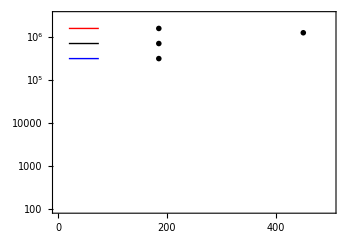

```mathematica
MyFrame=LogPlot[10^-20,{t,0,600},PlotRange->{{0,500},{10^2,10^6.5}},PlotStyle->{Black,Red,Blue},Frame->True,Axes->False,AspectRatio->1/1.5,FrameStyle->Directive[Thickness[0.003],FontSize->15,FontFamily->"Times",Black],LabelStyle->{{FontFamily->"Helvetica"},{FontFamily->"Helvetica"}},FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"{\\rm Time \\,[days]}","\\rho_a/\\rho_\\odot","",""},FrameTicks->{{{{1,Superscript[10,0]},{10^1,Superscript[10,1]},{10^2,Superscript[10,2]},{10^3,Superscript[10,3]},{10^4,Superscript[10,4]},{10^5,Superscript[10,5]},{10^6,Superscript[10,6]},{10^8,Superscript[10,8]},{10^10,Superscript[10,10]}},{{1,""},{10^1,""},{10^2,""},{10^3,""},{10^4,""},{10^5,""},{10^6,""},{10^8,""},{10^10,""}}},{{{0,0},{100,100},{200,200},{300,300},{400,400},{500,500},{600,600},{700,""},{800,800},{900,""},{1000,1000}},{{0,""},{100,""},{200,""},{300,""},{400,""},{500,""},{600,""},{700,""},{800,""},{900,""},{1000,""}}}},PlotRangeClipping->True,PlotRangePadding->None,
ImageSize->350,ImagePadding->{{65,15},{50,10}}];
PlotNFW1001=Block[{M=10^-10,d=1,x=0.1,DD=√(1-0.1^2)},LogPlot[{rhoNFW[t,M,d,x,DD]},{t,tmin[M,x,DD],tmax[M,x,DD]},PlotRange->All,PlotStyle->{Red,Thick}]];
PlotNFW1010=Block[{M=10^-10,d=1,x=0.5,DD=√(1-0.5^2)},LogPlot[{rhoNFW[t,M,d,x,DD]},{t,tmin[M,x,DD],tmax[M,x,DD]},PlotRange->All,PlotStyle->{Black,Thick}]];
PlotNFW1201=Block[{M=10^-12,d=1,x=0.1,DD=√(1-0.1^2)},LogPlot[{rhoNFW[t,M,d,x,DD]},{t,tmin[M,x,DD],tmax[M,x,DD]},PlotRange->All,PlotStyle->{Blue,Thick}]];
Labels=LogPlot[{10^6.2,10^5.85,10^5.5},{t,20,75},PlotRange->All,PlotStyle->{{Red,Thick},{Black,Thick},{Blue,Thick}}];
PlotEarthNFW=Show[MyFrame,PlotNFW1001,PlotNFW1010,PlotNFW1201,Labels,Graphics[Text[MaTeX["M=10^{-10}\\,M_\\odot\\,, \\,b=0.1\\,R_{\\rm AMC}",Magnification->0.8],{185,Log[10^6.2]}]],Graphics[Text[MaTeX["M=10^{-10}\\,M_\\odot\\,, \\,b=0.5\\,R_{\\rm AMC}",Magnification->0.8],{185,Log[10^5.85]}]],Graphics[Text[MaTeX["M=10^{-12}\\,M_\\odot\\,, \\,b=0.1\\,R_{\\rm AMC}",Magnification->0.8],{185,Log[10^5.5]}]],Graphics[Text[MaTeX["{\\rm NFW}",Magnification->1],{450,Log[10^6.1]}]]]
```

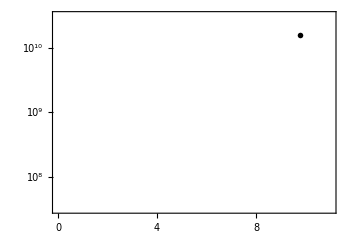

```mathematica
MyFrame=LogPlot[10^-20,{t,0,15},PlotRange->{{0,11},{10^7.5,10^10.5}},PlotStyle->{Black,Red,Blue},Frame->True,Axes->False,AspectRatio->1/1.5,
FrameStyle->Directive[Thickness[0.003],FontSize->15,FontFamily->"Times",Black],
LabelStyle->{{FontFamily->"Helvetica"},{FontFamily->"Helvetica"}},FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"{\\rm Time \\,[days]}","\\rho_a/\\rho_\\odot","",""},FrameTicks->{{{{1,Superscript[10,0]},{10^2,Superscript[10,2]},{10^4,Superscript[10,4]},{10^6,Superscript[10,6]},{10^7,Superscript[10,7]},{10^8,Superscript[10,8]},{10^9,Superscript[10,9]},{10^10,Superscript[10,10]}},{{1,""},{10^2,""},{10^4,""},{10^6,""},{10^8,""},{10^9,""},{10^10,""}}},{{{0,0},{2,2},{4,4},{6,6},{8,8},{10,10},{12,12}},{{0,""},{2,""},{4,""},{6,""},{8,""},{10,""},{12,""}}}},PlotRangeClipping->True,PlotRangePadding->None,
ImageSize->350,ImagePadding->{{65,15},{50,10}}];
PlotPL1001=Block[{M=10^-10,d=1,x=0.1,DD=√(1-0.1^2)},LogPlot[{rhoPL[t,M,d,x,DD]},{t,tminPL[M,x,DD],tmaxPL[M,x,DD]},PlotRange->All,PlotStyle->{Red,Thick}]];
PlotPL1010=Block[{M=10^-10,d=1,x=0.5,DD=√(1-0.5^2)},LogPlot[{rhoPL[t,M,d,x,DD]},{t,tminPL[M,x,DD],tmaxPL[M,x,DD]},PlotRange->All,PlotStyle->{Black,Thick}]];
PlotPL1201=Block[{M=10^-12,d=1,x=0.1,DD=√(1-0.1^2)},LogPlot[{rhoPL[t,M,d,x,DD]},{t,tminPL[M,x,DD],tmaxPL[M,x,DD]},PlotRange->All,PlotStyle->{Blue,Thick}]];
PlotEarthPL=Show[MyFrame,PlotPL1001,PlotPL1010,PlotPL1201,Graphics[Text[MaTeX["{\\rm PL}",Magnification->1],{9.75,Log[10^10.2]}]]]
```